```mathematica
(*Mathematica*)
```

```mathematica
{Z0,Z1,Z2,Z3}={0,1,x+I*y,z+t}
```

{0,1,x+ⅈ y,t+z}

```mathematica
m=(i/Sqrt[2])*{{z+y,x+I*y},{x-I*y,-z+t}}
```

{{(i (y+z))/(√2),(i (x+ⅈ y))/(√2)},{(i (x-ⅈ y))/(√2),(i (t-z))/(√2)}}

```mathematica
w=ExpandAll[{Z0,Z1}-m.{Z2,Z3}]
```

{-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)-(ⅈ i y^2)/(√2)-√2 i x z-ⅈ √2 i y z,1-(i t^2)/(√2)-(i x^2)/(√2)-(i y^2)/(√2)+(i z^2)/(√2)}

```mathematica
{Z0b,Z1b,Z2b,Z3b}={1,0,x-I*y,-z+t}
```

{1,0,x-ⅈ y,t-z}

```mathematica
v=ExpandAll[{Z0b,Z1b}-m.{Z2b,Z3b}]
```

{1-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)+(ⅈ i y^2)/(√2)+ⅈ √2 i y z,-(i t^2)/(√2)-(i x^2)/(√2)+ⅈ √2 i x y+(i y^2)/(√2)+√2 i t z-(i z^2)/(√2)}

```mathematica
u=Join[w,v]
```

{-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)-(ⅈ i y^2)/(√2)-√2 i x z-ⅈ √2 i y z,1-(i t^2)/(√2)-(i x^2)/(√2)-(i y^2)/(√2)+(i z^2)/(√2),1-(i t x)/(√2)-(ⅈ i t y)/(√2)-(i x y)/(√2)+(ⅈ i y^2)/(√2)+ⅈ √2 i y z,-(i t^2)/(√2)-(i x^2)/(√2)+ⅈ √2 i x y+(i y^2)/(√2)+√2 i t z-(i z^2)/(√2)}

```mathematica
Solve[Table[u[[i]]==0,{i,4}],{x,y,z,t}]
```

{{x→-(1/2-ⅈ)/(2^(3/4) √3),y→-(1+ⅈ/2)/(2^(3/4) √3),z→(1/5-(11 ⅈ)/10)/(2^(3/4) √3),t→(11/5-ⅈ/10)/(2^(3/4) √3)},{x→(1/2-ⅈ)/(2^(3/4) √3),y→(1+ⅈ/2)/(2^(3/4) √3),z→-(1/5-(11 ⅈ)/10)/(2^(3/4) √3),t→-(11/5-ⅈ/10)/(2^(3/4) √3)}}

```mathematica
s={x,y,z,t}/.NSolve[Table[u[[i]]==0,{i,4}],{x,y,z,t}]
```

{{-0.171647+0.343295 ⅈ,-0.343295-0.171647 ⅈ,0.0686589-0.377624 ⅈ,0.755248-0.0343295 ⅈ},{0.171647-0.343295 ⅈ,0.343295+0.171647 ⅈ,-0.0686589+0.377624 ⅈ,-0.755248+0.0343295 ⅈ}}

```mathematica
Abs[s]
```

{{0.383815,0.383815,0.383815,0.756028},{0.383815,0.383815,0.383815,0.756028}}

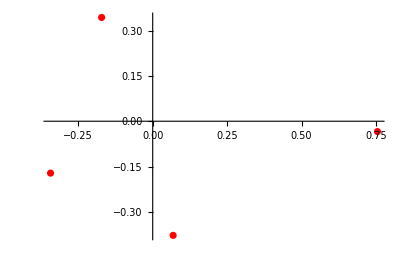
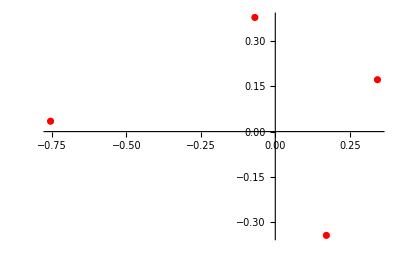

```mathematica
Table[ComplexListPlot[s[[i]],PlotStyle->Red],{i,2}]
```

```mathematica
Table[Sum[s[[i,j]],{j,4}],{i,2}]
```

{0.308965-0.240306 ⅈ,-0.308965+0.240306 ⅈ}

```mathematica
Abs[%]
```

{0.391416,0.391416}

```mathematica
Table[Sum[s[[i,j]]^2,{j,3}]-s[[i,4]]^2,{i,2}]//Chop
```

{-0.707107,-0.707107}

```mathematica
(* solutions as Killing vectors in a Cartan matrix*)
```

```mathematica
ca=Table[2*s[[i]].s[[j]]/(s[[i]].s[[i]]),{i,2},{j,2}]//Chop
```

{{2.,-2.},{-2.,2.}}

```mathematica
Grid[ca]
```

2. | -2.
-2. | 2.

```mathematica
Eigenvalues[ca]//Chop
```

{4.,0}

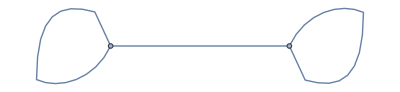

```mathematica
WeightedAdjacencyGraph[ca]
```

```mathematica
(*end*)
```